## Divergent color map examples

```mathematica
Needs["DivergentColorMaps`"]
```

I’ve taken the liberty of converting the pseudocode from Moreland’s paper into a package. I had to change the numerical values of the RGB->XYZ transformation matrix to account for the fact that Mathematica uses different reference white points for the different color spaces.

First we need a function to test various color maps,

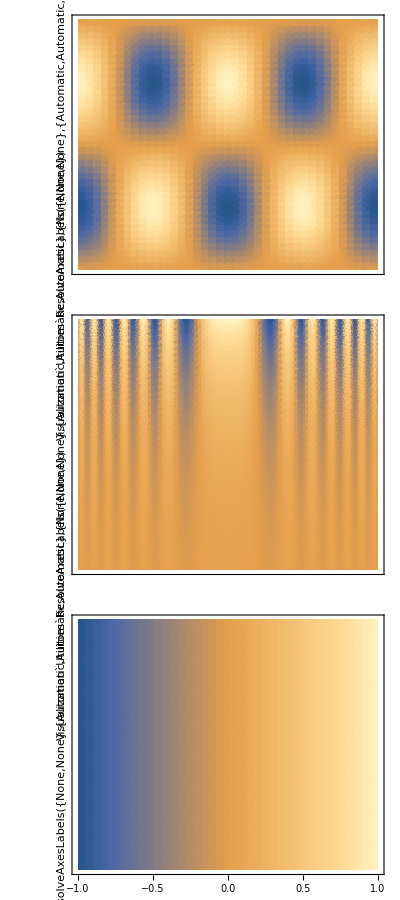

```mathematica
showcolorfunction[color_]:=With[{opts={PlotRange->All,ColorFunction->color,PlotPoints->40,PlotRangePadding->None,ImageSize->200}},Column[{DensityPlot[Cos[x] Sin[y],{x,-2 π,2 π},{y,-π,π},FrameTicks->None,AspectRatio->1/4,opts],DensityPlot[10 Cos[x^2] Exp[y],{x,-2 π,2 π},{y,-π,0},FrameTicks->None,AspectRatio->1/2,opts],DensityPlot[x,{x,-1,1},{y,0,1},FrameTicks->{{None,None},{Automatic,None}},AspectRatio->1/10,opts]},Center,0]];
showcolorfunction[Automatic] 
(*This will demonstrate the default color mapping Mathematica uses for density plots *)
```

These are the public functions from the package, and their usage

```mathematica
?DivergentColorFunc
?CoolToWarm
?DivergentColorScheme
?DivergentMaps
```

DivergentColorFunc[{r1,g1,b1},{r2,b2,g2}] returns a continuously diverging color map which interpolates between two RGB colors.

DivergentColorFunc[color1, color2] takes two color objecst as input and returns a continuously diverging color map.

Cool2Warm[n] gives the cool to warm color map, with n taking values between 0 and 1

DivergentColorScheme[scheme] gives a diverging color map which interpolates between the starting and ending colors in a builtin scheme

DivergentMaps is list of four divergent color maps used in http://www.kennethmoreland.com/color-maps/ColorMapsExpanded.pdf . divergentMaps[[1]] is equivalent to Cool2Warm

### example 1 - Divergent color maps defined explicitly

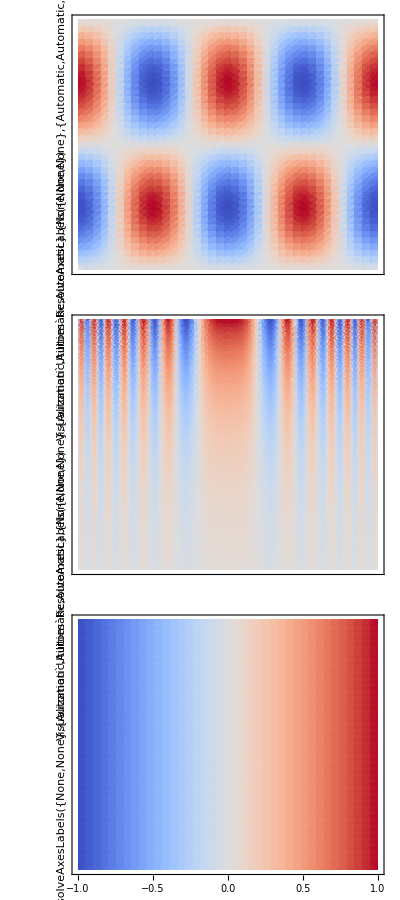

```mathematica
showcolorfunction@CoolToWarm
```

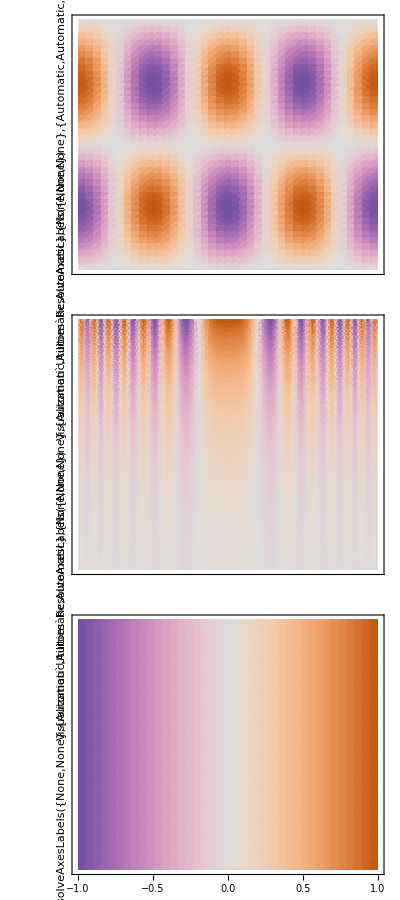
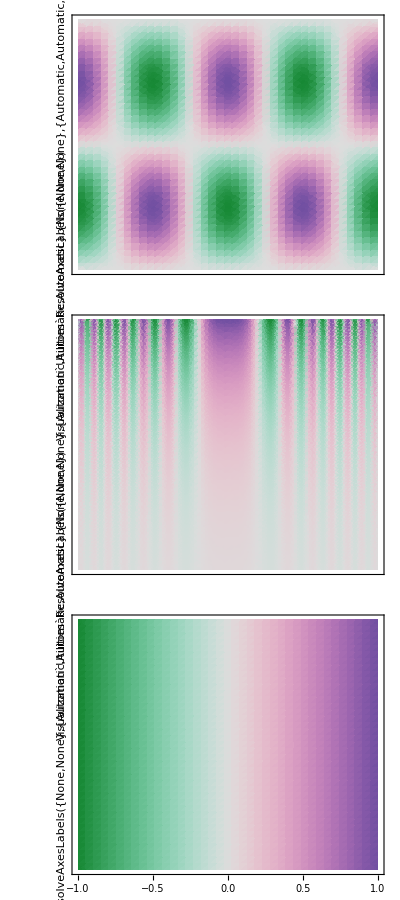
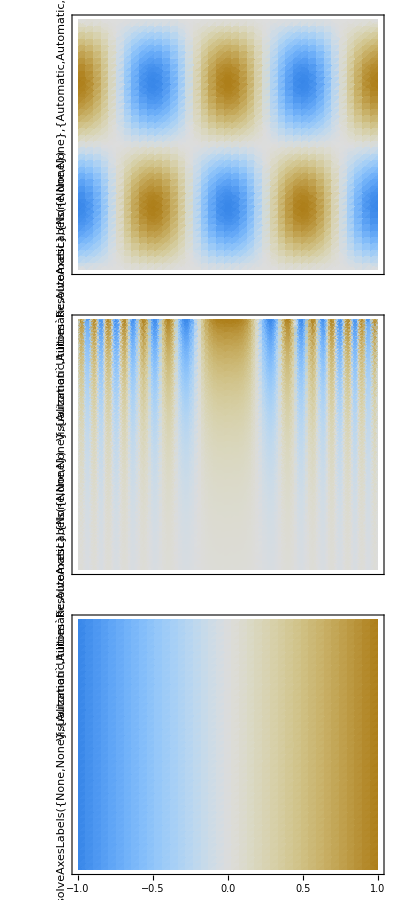
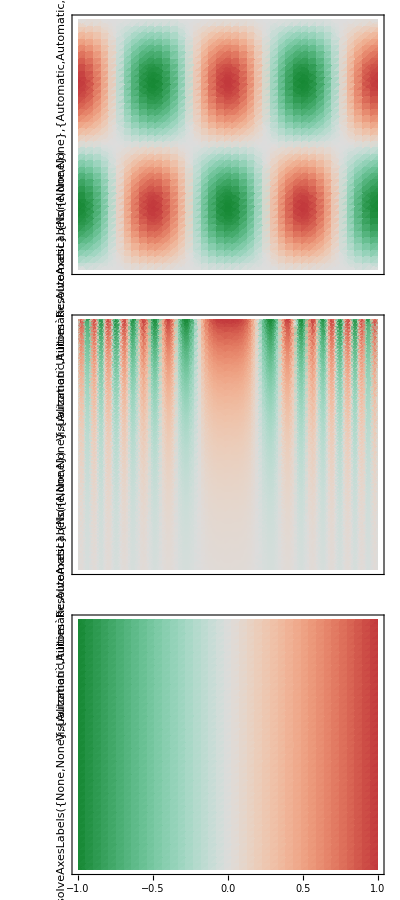
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
showcolorfunction/@DivergentMaps
```

### example 2 - Create a color map from two colors from any color space

DivergentColorFunc can take 2 lists of RGB values (from 0 to 1) as input, and will return a function.

Blend[{RGBColor[0, 0, 0.5],RGBColor[0.26609589398492084, 0.08007525972359264, 0.5922504049558679],RGBColor[0.4298793523328444, 0.17719161572853834, 0.6743578004106204],RGBColor[0.5729759601301336, 0.27799130357864793, 0.744425049369518],RGBColor[0.697288032897918, 0.38114744624478536, 0.8012151117473115],RGBColor[0.7996488404363518, 0.483724235879263, 0.8441210442858231],RGBColor[0.8761825892044287, 0.5822839611844938, 0.8731170292570879],RGBColor[0.9233782310118278, 0.6732084248234815, 0.8886869811376109],RGBColor[0.9384740521292996, 0.7529024631799797, 0.8917309925934408],RGBColor[0.9195584690251213, 0.8179723063386715, 0.8834514407921751],RGBColor[0.8654236525430442, 0.8653930898068188, 0.8652220017562685],RGBColor[0.8551007997545947, 0.8362858165948269, 0.7615756064886231],RGBColor[0.8430737690933491, 0.7903632726401254, 0.6515674864629587],RGBColor[0.8269842169934044, 0.7296806085503054, 0.5401898733994124],RGBColor[0.8048082492171514, 0.6564831073685294, 0.43184693820787823],RGBColor[0.7750457561741582, 0.5730931060115919, 0.3302078377647361],RGBColor[0.7367793654938628, 0.48174019728309975, 0.23815132947567969],RGBColor[0.6896649050423533, 0.3842471743872574, 0.15782797942801458],RGBColor[0.6338950711829605, 0.2812335590878786, 0.09092461293717938],RGBColor[0.5701555371694634, 0.16887836673615014, 0.03941146650319433],RGBColor[0.49999999999999994, 0, 0]},#1]&

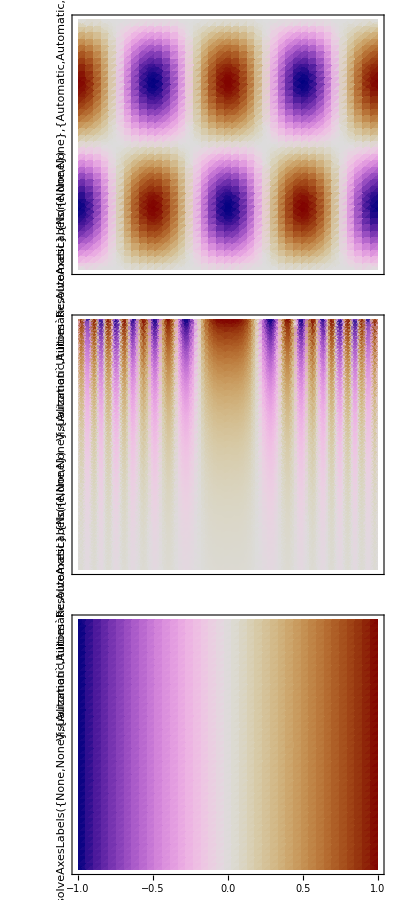

```mathematica
newcolorfunc=DivergentColorFunc[{0,0,.5},{.5,0,0}]
showcolorfunction@newcolorfunc
```

It can also take any color objects as input - as you can see, not all color combinations are suitable for a divergent gradient,

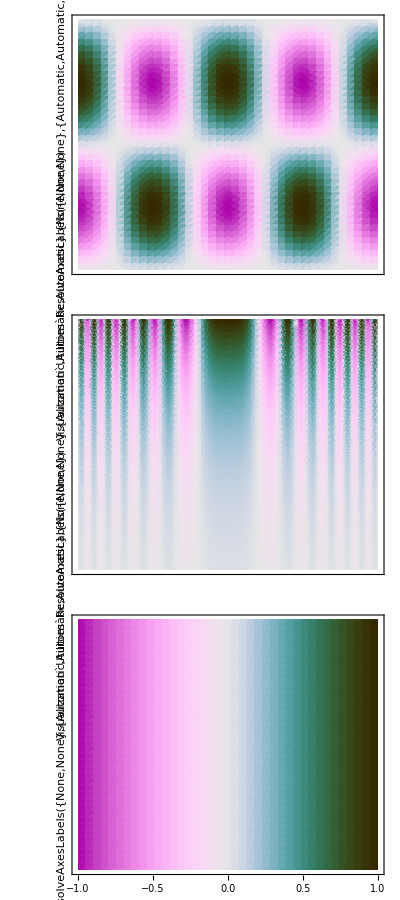
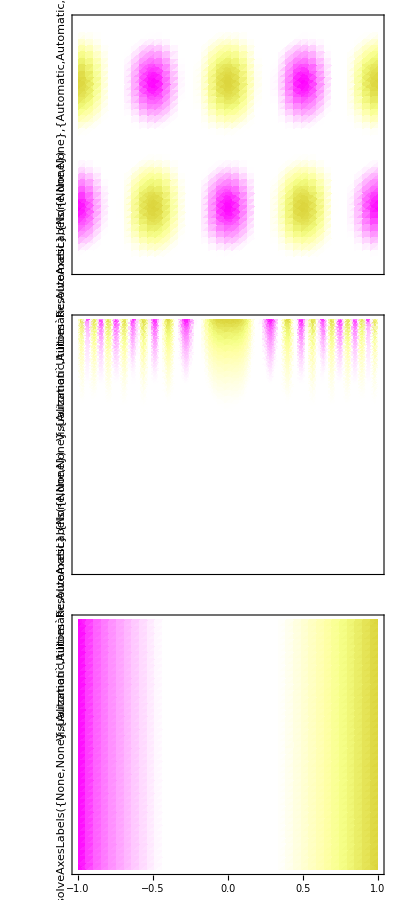
{-Graphics-,-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-}

```mathematica
{showcolorfunction@DivergentColorFunc[Darker[XYZColor[1,0.2,1]],LUVColor[.16,.5,1]],
showcolorfunction@DivergentColorFunc[Magenta,RGBColor[0.86, 0.8300000000000001, 0.23]],
showcolorfunction@DivergentColorFunc[LUVColor[0.5,1.816,0.8],LABColor[0.835,0.095,0.61]],
showcolorfunction@DivergentColorFunc[GrayLevel[1],GrayLevel[0]]}
```

### example 3 - Create a divergent color map by using the end colors from a pre-defined color map

```mathematica
showcolorfunction/@(DivergentColorScheme/@{"RoseColors","AvocadoColors","ThermometerColors","Rainbow"})
```

{-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-,-Graphics-
-Graphics-
-Graphics-}

### example 4 - usage in a standard Density or Contour plot

Using these color maps is just like using a built in color function,

```mathematica
DensityPlot[Sin[x-y] Exp[-.1(x+y)^2],{x,-4,4},{y,-5,5},ColorFunction->CoolToWarm,PlotLegends->Automatic,PlotPoints->50]
```

-Graphics-

In the above example, the function is symmetric about the zero point, which is how these divergent maps are intended to be used.  If the function has more positivet than negative features, or vice versa, it is necessary to rescale the inputs to the color function in order to keep the midpoint of the map at the zero value.

```mathematica
With[{cf = (CoolToWarm[Rescale[#,{-1,1}]]&)},
DensityPlot[Sinc[x-y] Exp[-.1(x+y)^2],{x,-4,4},{y,-5,5},PlotPoints->50
,ColorFunction->cf,ColorFunctionScaling->False,PlotLegends->BarLegend[{cf,{-1,1}}]]
]
```

-Graphics-